```mathematica
year = 2016;

angle:= Function[ (* params: hour of day*100, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[#3,{#1/100}]];
(* remove degree unit, then convert to radians *)
Subscript[γ, s]= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
Subscript[γ, s] = Subscript[γ, s] - Pi;
Subscript[θ, s]= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
Subscript[γ, p] = 0 * Pi/180; (* Solar panels azimuth *)
Subscript[θ, p] = #2 * Pi/180; (* Solar panels angle with horizontal *)
a= ArcCos[Cos[Subscript[γ, p]-Subscript[γ, s]] Cos[Subscript[θ, s]] Sin[Subscript[θ, p]]+Cos[Subscript[θ, p]] Sin[Subscript[θ, s]]]
]

directPower  := Function[ (* param: hour of day*100, solar panel angle in degrees, date. returns W/m^2 *)
Subscript[θ, z]=angle[#1,#2,#3]; (* solar zenith (misalignment) in radians *)
n= QuantityMagnitude[Quantity[#3 - DateObject[{year,1,1}]]]; (* day of year *)
Subscript[I, 0]= 1367 (1+0.034 Cos[360*n/365.25]);
Subscript[a, 0] = 0.4237 - 0.00821 36;
Subscript[a, 1] = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[Subscript[θ, z]]<0,
Subscript[I, direct]=0,
Subscript[I, direct] = Subscript[I, 0] (Subscript[a, 0] + Subscript[a, 1] E^(-k/Cos[Subscript[θ, z]])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
]
]

sumOverDay:=Function[ (* params: solar panel angle in degrees, date 
returns sum of solar power over the day at every hour*)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,#2];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,#2];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* Times 100 so the sum starts closer to the real sunUpHour, and not floors it to an integer when calculating the sum. Otherwise weird jumps in graphs appear when the sunUpHour jumps one hour *)
Sum[directPower[h,#1,#2],{h,sunriseHour*100,sunsetHour*100,10}]
]

dayAngle := Function[ (* params: day of month, month, returns optimal angle for this day *)
date = DateObject[{year,#2,#1}];
(* Find for which angle of the solar panels this value is maximal,starting at 50 *)
x /. FindMaximum[sumPowerLoss[x,date],{x,50,0,90}, AccuracyGoal->5][[2]]
]

monthAngle := Function [ (* params: month, returns optimal angle for a specific month by taking the average  *)
(* Count how many days are in this month *)
days = With[{first=DateObject[{year,#1,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]] ;
Sum[day[x,#1],{x,1,days}]/days
]


(******************************** END OF FUNCTIONS  ********************************)

(*angle[1400,40,DateObject[{2016,7,18}]]*180/Pi
directPower[1400,30,DateObject[{2016,7,18}]]*)
(*directPower[1500,0,DateObject[{2016,7,18}]]
directPower[1500,10,DateObject[{2016,7,18}]]
 DiscretePlot[directPower[x,0,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 DiscretePlot[directPower[x,10,DateObject[{2016,7,18}]],{x,500,2300,10},ImageSize -> Large] 
 sumOverDay[0,DateObject[{2016,7,18}]] 
 sumOverDay[10,DateObject[{2016,7,18}]] *)

(*DiscretePlot[sumOverDay[a,DateObject[{2016,7,18}]],{a,0,90,10}]*)

(***** END OF DEBUG ******)

(* Graph for a day *)
(* date = DateObject[{2016,7,18}];
 AbsoluteTiming[DiscretePlot[sumOverDay[x,date],{x,0,90,10},ImageSize->Large,AxesLabel -> {"Solar panel angle", "Total of sun power, W/m^2"}] ] *)

(* Graph for a month *)
 (* month = 6;
days = With[{first=DateObject[{year,month,1}]},DayCount[first,DatePlus[first,{{1,"Month"}}]]];
AbsoluteTiming[DiscretePlot[dayAngle[a,month],{a,1,days},ImageSize->Large,AxesLabel -> {"Day", "Optimal angle"}]] *)
dayAngle[18,7]

(* Graph for this year *)
(* AbsoluteTiming[DiscretePlot[monthAngle[x],{x,1,12},ImageSize->Large,AxesLabel -> {"Month", "Average of optimal angle"}] ] *)
```

FindMinimum::reged: The point {90.} is at the edge of the search region {0.,90.} in coordinate 1 and the computed search direction points outside the region.

90.

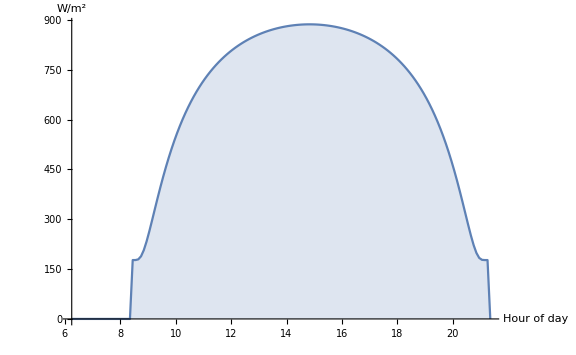
```mathematica
8/6,30 panel angle-Graphics-
```

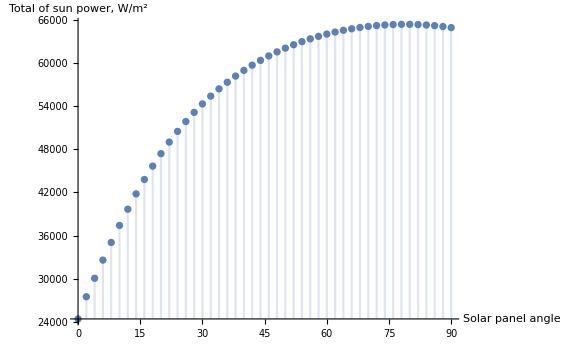
```mathematica
december first:-Graphics-
```

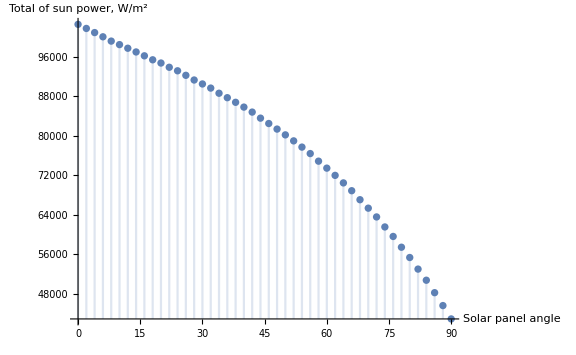
```mathematica
20/6 -Graphics-
```